# Tight Binding Model for Studying the Effect of Spin-Orbit Coupling in Multi-layers in the Frame of Linear Response theory

```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["GreenSlab`"];
```

Welcome to GreenSlab.
		G | RGBColor[0, 1, 1] | 0 | 0 | 0 | 0 | 0 | 0 | 0
RGBColor[0, 1, 1] | R | RGBColor[1, Rational[1, 2], Rational[1, 2]] | 0 | 0 | 0 | 0 | 0 | 0
0 | RGBColor[1, Rational[1, 2], Rational[1, 2]] | E | RGBColor[0, 1, 0] | 0 | 0 | 0 | 0 | 0
0 | 0 | RGBColor[0, 1, 0] | E | RGBColor[0, 1, 0] | 0 | 0 | 0 | 0
0 | 0 | 0 | RGBColor[0, 1, 0] | N | RGBColor[0, Rational[2, 3], Rational[2, 3]] | RGBColor[0, Rational[2, 3], Rational[2, 3]] | 0 | 0
0 | 0 | 0 | 0 | RGBColor[0, Rational[2, 3], Rational[2, 3]] | S | RGBColor[0, 0, 1] | RGBColor[1, 0.5, 0] | RGBColor[1, 0.5, 0]
0 | 0 | 0 | 0 | RGBColor[0, Rational[2, 3], Rational[2, 3]] | RGBColor[0, 0, 1] | L | RGBColor[1, 0.5, 0] | RGBColor[1, 0.5, 0]
0 | 0 | 0 | 0 | 0 | RGBColor[1, 0.5, 0] | RGBColor[1, 0.5, 0] | A | RGBColor[0, 0, 1]
0 | 0 | 0 | 0 | 0 | RGBColor[1, 0.5, 0] | RGBColor[1, 0.5, 0] | RGBColor[0, 0, 1] | B

The package will help you to build a slab Hamiltonian
for a given number of layers.
You can construct the retarded or advanced Greens function
and use it in Linear Response Theory.
It can also calculate normal band structure and band structure with 
a weight corresponding to an operator.

While calling the the inbuilt functions use them in a definition rather than
in a function. For example use
		 f[kx_]=Combine[Cos[kx],-Cos[kx],1]
not	  f[kx_]:=Combine[Cos[kx],-Cos[kx],1]

Type Info[GreenSlab] to see all available functions and info[function_name]
to get information about a particular function.

Sumit Ghosh 04-06-2018 V1.0 (sumit.ghosh@kaust.edu.sa)

```mathematica
Info[GreenSlab]
```

A collection of small codes to build and study layered hamiltonians. It contains

  1. GreenSlab |   2. Slab |   3. LSlab
  4. Matview |   5. Getblock |   6. Takeblock
  7. Makeblock |   8. Replblock |   9. Combine
 10. Checkvars |  11. Checkfunc |  12. Bands
 13. WBands |  14. Gr |  15. Ga 

Use Info[function] for their details.

## Parameters

```mathematica
Clear[VsF,VdF,VpF,VsN,VdN,VpN,VsFN,VdFN,VpFN,a0,ExyF,ExzF,EyzF,ExyN,ExzN,EyzN,JxyF,JxzF,JyzF,V0n,Vn,Vf,J,xi,eta,th,fi,G,hbar,ehbar,n,Nn,Ef,L,ch]
nbF =3;
nbN= 6;
ch[i_]:=xi;
(*Slater-Koster 2-center parameters,  Orthogonal, 1rst neighbor and 2nd neighbor Handbook of the Band Structure of Elemental Solids, we use iron and tungsten as they are bcc*)
(*maybe not useful as we implement magnetization by hand*)

(*
VsF1up= -0.04541*13.6;(*Fe*) (*-0.0388*13.6Co up*)
VpF1up= 0.02714*13.6;(*Fe*) (*0.02387*13.6Co up*)
VdF1up= -0.00260*13.6;(*Fe*) (*-0.00384*13.6Co up*)
VsF1down= -0.05266*13.6 ;(*Fe*) (*-0.04403*13.6Co up*)
VpF1down=  0.03276*13.6;(*Fe*) (*0.02763*13.6Co up*)
VdF1down=-0.00286*13.6 ;(*Fe*) (*-0.00442*13.6Co up*)

VsF2up=-0.02713*13.6;(*Fe*) (*-0.00669*13.6 Co up*)
VpF2up=0.00589*13.6;(*Fe*) (*0.00167*13.6 Co up*)
VdF2up=0.00060*13.6;(*Fe*) (*0.00023*13.6 Co up*)
VsF2down=-0.03396*13.6;(*Fe*) (*-0.00793*13.6 Co down*)
VpF2down=0.00581*13.6;(*Fe*) (*0.00198*13.6 Co down*)
VdF2down=0.00114*13.6;(*Fe*) (*0.00026*13.6 Co down*)
*)
(*here we write our parameters*)
VsF1= -0.04541*13.6;(*Fe*) (*-0.0388*13.6Co up*)
VpF1= 0.02714*13.6;(*Fe*) (*0.02387*13.6Co up*)
VdF1= -0.00260*13.6;(*Fe*) (*-0.00384*13.6Co up*)

VsF2=-0.02713*13.6;(*Fe*) (*-0.00669*13.6 Co up*)
VpF2=0.00589*13.6;(*Fe*) (*0.00167*13.6 Co up*)
VdF2=0.00060*13.6;(*Fe*) (*0.00023*13.6 Co up*)

VsN1= -0.11837*13.6;(*W*) (* -0.06856*13.6 Pt fcc*)
VpN1= 0.05194*13.6; (*W*) (* 0.03528*13.6 Pt fcc*)
VdN1= 0.00248*13.6;(*W*) (* -0.00588*13.6 Pt fcc*)

VsN2= -0.07313*13.6;(*W*) 
VpN2= -0.01264*13.6; (*W*) 
VdN2= 0.00908*13.6;(*W*) 

VsFN1=-(0.04541+0.11837)*13.6/2; 
VpFN1=( 0.02714+0.05194)*13.6/2;
VdFN1=(-0.00260+0.00248)*13.6/2;

VsFN2=-(0.02713+0.07313)*13.6/2; 
VpFN2=( 0.00589 -0.01264)*13.6/2;
VdFN2=(0.00060+0.00908)*13.6/2;
(* -13.6 eV is the binding Energy of the elecron of the Hydrogen atom *)
a0=0.316*10^-9;(*m*)
ExyF=E0+t2gF;(*t2gFUp=0.64840*13.6,t2gFDn=0.78456*13.6*)
ExzF=E0+t2gF;(*t2gFUp=0.64840*13.6,t2gFDn=0.78456*13.6*)
EyzF=E0+t2gF;(*t2gFUp=0.64840*13.6,t2gFDn=0.78456*13.6*)
Ex2y2F=E0+egF;(*egFUp=0.62960*13.6, egFDn=0.75661*13.6*)
Ez2F=E0+egF;(*egFUp=0.62960*13.6, egFDn=0.75661*13.6*)
ExyN=t2gN;(*t2gN=0.96813*13.6*)
ExzN=t2gN;(*t2gN=0.96813*13.6*)
EyzN=t2gN;(*t2gN=0.96813*13.6*)
Ex2y2N=egN;(*egN=0.85720*13.6*)
Ez2N=egN;(*egN=0.85720*13.6*)

JxyF=Jt2g;
JxzF=Jt2g;
JyzF=Jt2g;
Jx2y2F=Jeg;
Jz2F=Jeg;

t2gN=0.96813*13.6;
egN=0.85720*13.6;
E0=4.0;
t2gF=(0.64840*13.6+0.78456*13.6)/2;
egF=(0.62960*13.6+0.75661*13.6)/2;

Jt2g=(0.64840*13.6-0.78456*13.6);
Jeg=Jt2g;
(*Jeg=(0.62960*13.6-0.75661*13.6);*)

xi=0.014*13.6;(*0.36 W*) (*0.4 Pt*) (* 0.065 Co*)(*in Solid State Physics by Aurelien*)

eta=Pi/4;

th=0;
fi=0;

hbar=6.58*10^-16;(*eV.s*)
ehbar=6.58*10^-16*1.6*10^-19;

Ef=14.0; (* eV /real Fermi energy of Tungsten: 11eV*)
G=0.05;
muB=5.788*10^-5;(*eV/Oe*)
Vmag=muB*ee/(Ms*L*a0);(*m^2 - see below*)

ee=1.6*10^-19;
Ms=800*10^3;(*A/m*)

L=3;
n=100;
```

Some standard values: Ef=1.5, V0=-1, J=1; then play around; typical effective magnetic volume is \muB/(Msd)=1.157x10^-20 m^2, with Ms=800emu/cc, d=1nm
Then, the test formula is (J/muB)*(muB/Msd)*IntISGE/(Cxx/d)*10^12...this gives the torque efficiency in Oe/(10^8A/cm2).
The effective spin Hall conductance reads J*IntISGE*(2*e/hbar)*10^-4...this gives the spin Hall conductivity in (\hbar/2e) 10^4 Ohm^-1.m^-1

Note: looks like n=300 is the best, but n=200 is ok; n=100 is too small

## Hopping parameters according to Slater Koster

```mathematica
gxyF[kx_,ky_]:=(3*VsF2+VdF2)/2*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gxzF[kx_,ky_]:=(VpF2+VdF2)*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gyzF[kx_,ky_]:=(VpF2+VdF2)*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gx2y2F[kx_,ky_]:= 2*VpF2 *(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gz2F[kx_,ky_]:=  (VsF2+3*VdF2)/2*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gxyN[kx_,ky_]:=(3*VsN2+VdN2)/2*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gxzN[kx_,ky_]:=(VpN2+VdN2)*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gyzN[kx_,ky_]:=(VpN2+VdN2)*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gx2y2N[kx_,ky_]:= 2*VpN2 *(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gz2N[kx_,ky_]:=  (VsN2+3*VdN2)/2*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);

TxyFxzF[kx_,ky_]:=0;
TxyFyzF[kx_,ky_]:=0;
TxzFyzF[kx_,ky_]:=(VpF2-VdF2)*(Cos[(kx+ky)*a0/2]-Cos[(kx-ky)*a0/2]);
TxyFx2y2F[kx_,ky_]:=0;
TyzFx2y2F[kx_,ky_]:=0;
TxzFx2y2F[kx_,ky_]:=0;
Tz2Fx2y2F[kx_,ky_]:=0;
TxyFz2F[kx_,ky_]:=-Sqrt[3]/2*(VsF2-VdF2)*(Cos[(kx+ky)*a0/2]-Cos[(kx-ky)*a0/2]);
TyzFz2F[kx_,ky_]:=0;
TxzFz2F[kx_,ky_]:=0;

TxyNxzN[kx_,ky_]:=0;
TxyNyzN[kx_,ky_]:=0;
TxzNyzN[kx_,ky_]:=(VpN2-VdN2)*(Cos[(kx+ky)*a0/2]-Cos[(kx-ky)*a0/2]);
TxyNx2y2N[kx_,ky_]:=0;
TyzNx2y2N[kx_,ky_]:=0;
TxzNx2y2N[kx_,ky_]:=0;
Tz2Nx2y2N[kx_,ky_]:=0;
TxyNz2N[kx_,ky_]:=-Sqrt[3]/2*(VsN2-VdN2)*(Cos[(kx+ky)*a0/2]-Cos[(kx-ky)*a0/2]);
TyzNz2N[kx_,ky_]:=0;
TxzNz2N[kx_,ky_]:=0;

TxyFxyN[kx_,ky_]:=2*(VpFN1*Cos[eta]^2+VdFN1*Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);
TyzFyzN[kx_,ky_]:=2*(VpFN1*Sin[eta]^2+VdFN1*Cos[eta]^2)*Cos[kx*a0/2]+2*((3*VsFN1+VdFN1-4*VpFN1)*Sin[eta]^2*Cos[eta]^2+VpFN1)*Cos[ky*a0/2];
TxzFxzN[kx_,ky_]:=2*(VpFN1*Sin[eta]^2+VdFN1*Cos[eta]^2)*Cos[ky*a0/2]+2*((3*VsFN1+VdFN1-4*VpFN1)*Sin[eta]^2*Cos[eta]^2+VpFN1)*Cos[kx*a0/2];
TxzFyzN[kx_,ky_]:=0;
TyzFxzN[kx_,ky_]:=0;
TxyFxzN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpFN1-VdFN1)*Sin[ky*a0/2];
TxyFyzN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpFN1-VdFN1)*Sin[kx*a0/2];
TxzFxyN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpFN1-VdFN1)*Sin[ky*a0/2];
TyzFxyN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpFN1-VdFN1)*Sin[kx*a0/2];
TxyFx2y2N[kx_,ky_]:=0;
TyzFx2y2N[kx_,ky_]:=I/4* (-3 VdFN1+3 VsFN1+(VdFN1-4 VpFN1+3 VsFN1) Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2];
TxzFx2y2N[kx_,ky_]:=-I/4* (-3 VdFN1+3 VsFN1+(VdFN1-4 VpFN1+3 VsFN1) Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2];
Tz2Fx2y2N[kx_,ky_]:= -1/2 *√3 Cos[eta]^2 *(-VdFN1+VsFN1 Cos[eta]^2-(VdFN1-4 VpFN1+2 VsFN1) Sin[eta]^2)*Cos[kx*a0/2]+1/4* √3 Cos[eta]^2 (-3 VdFN1+4 VpFN1-VsFN1+(VdFN1-4 VpFN1+3 VsFN1) Cos[2 eta])*Cos[ky*a0/2];
Tx2y2Fx2y2N[kx_,ky_]:= (3/2 VsFN1 Cos[eta]^4+(1/8) VdFN1 (-3+Cos[2 eta])^2+2VpFN1 Cos[eta]^2  Sin[eta]^2)* (Cos[kx*a0/2]+Cos[ky*a0/2])  ;
TxyFz2N[kx_,ky_]:= 0;
TyzFz2N[kx_,ky_]:= I/4*Sqrt[3]* (VdFN1-VsFN1+(VdFN1-4 VpFN1+3 VsFN1) *Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2] ;
TxzFz2N[kx_,ky_]:= I/4*Sqrt[3]*(VdFN1-VsFN1+(VdFN1-4 VpFN1+3 VsFN1)* Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2] ;
Tz2Fz2N[kx_,ky_]:=(3/2 VdFN1 Cos[eta]^4+1/8 VsFN1 (1-3 Cos[2 eta])^2+6 VpFN1 Cos[eta]^2 Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);

zTxyNxyN[kx_,ky_]:=2*(VpN1*Cos[eta]^2+VdN1*Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);
zTyzNyzN[kx_,ky_]:=2*(VpN1*Sin[eta]^2+VdN1*Cos[eta]^2)*Cos[kx*a0/2]+2*((3*VsN1+VdN1-4*VpN1)*Sin[eta]^2*Cos[eta]^2+VpN1)*Cos[ky*a0/2];
zTxzNxzN[kx_,ky_]:=2*(VpN1*Sin[eta]^2+VdN1*Cos[eta]^2)*Cos[ky*a0/2]+2*((3*VsN1+VdN1-4*VpN1)*Sin[eta]^2*Cos[eta]^2+VpN1)*Cos[kx*a0/2];
zTxzNyzN[kx_,ky_]:=0;
zTyzNxzN[kx_,ky_]:=0;
zTxyNxzN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpN1-VdN1)*Sin[ky*a0/2];
zTxyNyzN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpN1-VdN1)*Sin[kx*a0/2];
zTxzNxyN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpN1-VdN1)*Sin[ky*a0/2];
zTyzNxyN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpN1-VdN1)*Sin[kx*a0/2];
zTxyNx2y2N[kx_,ky_]:=0;
zTyzNx2y2N[kx_,ky_]:=I/4* (-3 VdN1+3 VsN1+(VdN1-4 VpN1+3 VsN1) Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2];
zTxzNx2y2N[kx_,ky_]:=-I/4* (-3 VdN1+3 VsN1+(VdN1-4 VpN1+3 VsN1) Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2];
zTz2Nx2y2N[kx_,ky_]:= -1/2 *√3 Cos[eta]^2 *(-VdN1+VsN1 Cos[eta]^2-(VdN1-4 VpN1+2 VsN1)* Sin[eta]^2)*Cos[kx*a0/2]+1/4* √3 Cos[eta]^2 (-3 VdN1+4 VpN1-VsN1+(VdN1-4 VpN1+3 VsN1)*Cos[2 eta])*Cos[ky*a0/2];
zTx2y2Nx2y2N[kx_,ky_]:=(3/2 VsN1 Cos[eta]^4+(1/8) VdN1 (-3+Cos[2 eta])^2+2VpN1 Cos[eta]^2  Sin[eta]^2)* (Cos[kx*a0/2]+Cos[ky*a0/2])  ;
zTxyNz2N[kx_,ky_]:= 0;
zTyzNz2N[kx_,ky_]:= I/4*Sqrt[3]* (VdN1-VsN1+(VdN1-4 VpN1+3 VsN1) *Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2] ;
zTxzNz2N[kx_,ky_]:= I/4*Sqrt[3]*(VdN1-VsN1+(VdN1-4 VpN1+3 VsN1)* Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2] ;
zTz2Nz2N[kx_,ky_]:=(3/2 VdN1 Cos[eta]^4+1/8 VsN1 (1-3 Cos[2 eta])^2+6 VpN1 Cos[eta]^2 Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);

zTxyFxyF[kx_,ky_]:=2*(VpF1*Cos[eta]^2+VdF1*Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);
zTyzFyzF[kx_,ky_]:=2*(VpF1*Sin[eta]^2+VdF1*Cos[eta]^2)*Cos[kx*a0/2]+2*((3*VsF1+VdF1-4*VpF1)*Sin[eta]^2*Cos[eta]^2+VpF1)*Cos[ky*a0/2];
zTxzFxzF[kx_,ky_]:=2*(VpF1*Sin[eta]^2+VdF1*Cos[eta]^2)*Cos[ky*a0/2]+2*((3*VsF1+VdF1-4*VpF1)*Sin[eta]^2*Cos[eta]^2+VpF1)*Cos[kx*a0/2];
zTxzFyzF[kx_,ky_]:=0;
zTyzFxzF[kx_,ky_]:=0;
zTxyFxzF[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpF1-VdF1)*Sin[ky*a0/2];
zTxyFyzF[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpF1-VdF1)*Sin[kx*a0/2];
zTxzFxyF[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpF1-VdF1)*Sin[ky*a0/2];
zTyzFxyF[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpF1-VdF1)*Sin[kx*a0/2];
zTxyFx2y2F[kx_,ky_]:=0;
zTyzFx2y2F[kx_,ky_]:=I/4* (-3 VdF1+3 VsF1+(VdF1-4 VpF1+3 VsF1) Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2];
zTxzFx2y2F[kx_,ky_]:=-I/4* (-3 VdF1+3 VsF1+(VdF1-4 VpF1+3 VsF1) Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2];
zTz2Fx2y2F[kx_,ky_]:= -1/2 *√3 Cos[eta]^2 *(-VdF1+VsF1 Cos[eta]^2-(VdF1-4 VpF1+2 VsF1) Sin[eta]^2)*Cos[kx*a0/2]+1/4* √3 Cos[eta]^2 (-3 VdF1+4 VpF1-VsF1+(VdF1-4 VpF1+3 VsF1) Cos[2 eta])*Cos[ky*a0/2];
zTx2y2Fx2y2F[kx_,ky_]:=(3/2 VsF1 Cos[eta]^4+(1/8) VdF1 (-3+Cos[2 eta])^2+2VpF1 Cos[eta]^2  Sin[eta]^2)* (Cos[kx*a0/2]+Cos[ky*a0/2])  ;
zTxyFz2F[kx_,ky_]:= 0;
zTyzFz2F[kx_,ky_]:= I/4*Sqrt[3]* (VdF1-VsF1+(VdF1-4 VpF1+3 VsF1) *Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2] ;
zTxzFz2F[kx_,ky_]:= I/4*Sqrt[3]*(VdF1-VsF1+(VdF1-4 VpF1+3 VsF1)* Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2] ;
zTz2Fz2F[kx_,ky_]:=(3/2 VdF1 Cos[eta]^4+1/8 VsF1 (1-3 Cos[2 eta])^2+6 VpF1 Cos[eta]^2 Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);
```

## Single Multilayer Hamiltonian

```mathematica
(*These are ferromagnet's building block matrices, each 10 by 10*)
MF[kx_,ky_]:={{ExyF+JxyF/2*Cos[th]+gxyF[kx,ky],JxyF/2*Exp[-I*fi]*Sin[th],TxyFxzF[kx,ky],0,TxyFyzF[kx,ky],0,TxyFz2F[kx,ky],0,TxyFx2y2F[kx,ky],0},{JxyF/2*Exp[I*fi]*Sin[th],ExyF-JxyF/2*Cos[th]+gxyF[kx,ky],0,TxyFxzF[kx,ky],0,TxyFyzF[kx,ky],0,TxyFz2F[kx,ky],0,TxyFx2y2F[kx,ky]},{TxyFxzF[kx,ky],0,ExzF+JxzF/2*Cos[th]+gxzF[kx,ky],JxzF/2*Exp[-I*fi]*Sin[th],TxzFyzF[kx,ky],0,TxzFz2F[kx,ky],0,TxzFx2y2F[kx,ky],0},{0,TxyFxzF[kx,ky],JxzF/2*Exp[I*fi]*Sin[th],ExzF-JxzF/2*Cos[th]+gxzF[kx,ky],0,TxzFyzF[kx,ky],0,TxzFz2F[kx,ky],0,TxzFx2y2F[kx,ky]},
{TxyFyzF[kx,ky],0,TxzFyzF[kx,ky],0,EyzF+JyzF/2*Cos[th]+gyzF[kx,ky],JyzF/2*Exp[-I*fi]*Sin[th],TyzFz2F[kx,ky],0,TyzFx2y2F[kx,ky],0},
{0,TxyFyzF[kx,ky],0,TxzFyzF[kx,ky],JyzF/2*Exp[I*fi]*Sin[th],EyzF-JyzF/2*Cos[th]+gyzF[kx,ky],0,TyzFz2F[kx,ky],0,TyzFx2y2F[kx,ky]},
{TxyFz2F[kx,ky],0,TxzFz2F[kx,ky],0,TyzFz2F[kx,ky],0,Ez2F+Jz2F/2*Cos[th]+gz2F[kx,ky],Jz2F/2*Exp[-I*fi]*Sin[th],Tz2Fx2y2F[kx,ky],0},
{0,TxyFz2F[kx,ky],0,TxzFz2F[kx,ky],0,TyzFz2F[kx,ky],Jz2F/2*Exp[I*fi]*Sin[th],Ez2F-Jz2F/2*Cos[th]+gz2F[kx,ky],0,Tz2Fx2y2F[kx,ky]},
{TxyFx2y2F[kx,ky],0,TxzFx2y2F[kx,ky],0,TyzFx2y2F[kx,ky],0,Tz2Fx2y2F[kx,ky],0,Ex2y2F+Jx2y2F/2*Cos[th]+gx2y2F[kx,ky],Jx2y2F/2*Exp[-I*fi]*Sin[th]},
{0,TxyFx2y2F[kx,ky],0,TxzFx2y2F[kx,ky],0,TyzFx2y2F[kx,ky],0,Tz2Fx2y2F[kx,ky],Jx2y2F/2*Exp[I*fi]*Sin[th],Ex2y2F-Jx2y2F/2*Cos[th]+gx2y2F[kx,ky]}};

Mff[kx_,ky_]:= {{zTxyFxyF[kx,ky],0,zTxyFxzF[kx,ky],0,zTxyFyzF[kx,ky],0,zTxyFz2F[kx,ky],0,zTxyFx2y2F[kx,ky],0},
{0,zTxyFxyF[kx,ky],0,zTxyFxzF[kx,ky],0,zTxyFyzF[kx,ky],0,zTxyFz2F[kx,ky],0,zTxyFx2y2F[kx,ky]},
{zTxzFxyF[kx,ky],0,zTxzFxzF[kx,ky],0,zTxzFyzF[kx,ky],0,zTxzFz2F[kx,ky],0,zTxzFx2y2F[kx,ky],0},
{0,zTxzFxyF[kx,ky],0,zTxzFxzF[kx,ky],0,zTxzFyzF[kx,ky],0,zTxzFz2F[kx,ky],0,zTxzFx2y2F[kx,ky]},
{zTyzFxyF[kx,ky],0,zTyzFxzF[kx,ky],0,zTyzFyzF[kx,ky],0,zTyzFz2F[kx,ky],0,zTyzFx2y2F[kx,ky],0},
{0,zTyzFxyF[kx,ky],0,zTyzFxzF[kx,ky],0,zTyzFyzF[kx,ky],0,zTyzFz2F[kx,ky],0,zTyzFx2y2F[kx,ky]},
{zTxyFz2F[kx,ky],0,zTxzFz2F[kx,ky],0,zTyzFz2F[kx,ky],0,zTz2Fz2F[kx,ky],0,zTz2Fx2y2F[kx,ky],0},
{0,zTxyFz2F[kx,ky],0,zTxzFz2F[kx,ky],0,zTyzFz2F[kx,ky],0,zTz2Fz2F[kx,ky],0,zTz2Fx2y2F[kx,ky]},
{zTxyFx2y2F[kx,ky],0,zTxzFx2y2F[kx,ky],0,zTyzFx2y2F[kx,ky],0,zTz2Fx2y2F[kx,ky],0,zTx2y2Fx2y2F[kx,ky],0},
{0,zTxyFx2y2F[kx,ky],0,zTxzFx2y2F[kx,ky],0,zTyzFx2y2F[kx,ky],0,zTz2Fx2y2F[kx,ky],0,zTx2y2Fx2y2F[kx,ky]}};

Mff2:={{VdF2,0,0,0,0,0,0,0,0,0},
{0,VdF2,0,0,0,0,0,0,0,0},
{0,0,VpF2,0,0,0,0,0,0,0},
{0,0,0,VpF2,0,0,0,0,0,0},
{0,0,0,0,VpF2,0,0,0,0,0},
{0,0,0,0,0,VpF2,0,0,0,0},
{0,0,0,0,0,0,VsF2,0,0,0},
{0,0,0,0,0,0,0,VsF2,0,0},
{0,0,0,0,0,0,0,0,VdF2,0},
{0,0,0,0,0,0,0,0,0,VdF2}};

Msoc = {{0,0,0,I,0,-1,0,0,2I,0},{0,0,I,0,1,0,0,0,0,-2I},{0,-I,0,0,-I,0,0,-Sqrt[3],0,1},{-I,0,0,0,0,I,Sqrt[3],0,-1,0},{0,1,I,0,0,0,0,I Sqrt[3],0,I},{-1,0,0,-I,0,0,I Sqrt[3],0,I,0},{0,0,0,Sqrt[3],0,-I Sqrt[3],0,0,0,0},{0,0,-Sqrt[3],0,-I Sqrt[3],0,0,0,0,0},{-2 I,0,0,-1,0,-I,0,0,0,0},{0,2 I,1,0,-I,0,0,0,0,0}};

(*These are metals' building block matrices, each 10 by 10*)
MN[kx_,ky_,i_]:={{ExyN+gxyN[kx,ky],0,TxyNxzN[kx,ky],0,TxyNyzN[kx,ky],0,TxyNz2N[kx,ky],0,TxyNx2y2N[kx,ky],0},
{0,ExyN+gxyN[kx,ky],0,TxyNxzN[kx,ky],0,TxyNyzN[kx,ky],0,TxyNz2N[kx,ky],0,TxyNx2y2N[kx,ky]},
{TxyNxzN[kx,ky],0,ExzN+gxzN[kx,ky],0,TxzNyzN[kx,ky],0,TxzNz2N[kx,ky],0,TxzNx2y2N[kx,ky],0},
{0,TxyNxzN[kx,ky],0,ExzN+gxzN[kx,ky],0,TxzNyzN[kx,ky],0,TxzNz2N[kx,ky],0,TxzNx2y2N[kx,ky]},
{TxyNyzN[kx,ky],0,TxzNyzN[kx,ky],0,EyzN+gyzN[kx,ky],0,TyzNz2N[kx,ky],0,TyzNx2y2N[kx,ky],0},
{0,TxyNyzN[kx,ky],0,TxzNyzN[kx,ky],0,EyzN+gyzN[kx,ky],0,TyzNz2N[kx,ky],0,TyzNx2y2N[kx,ky]},
{TxyNz2N[kx,ky],0,TxzNz2N[kx,ky],0,TyzNz2N[kx,ky],0,Ez2N+gz2N[kx,ky],0,Tz2Nx2y2N[kx,ky],0},
{0,TxyNz2N[kx,ky],0,TxzNz2N[kx,ky],0,TyzNz2N[kx,ky],0,Ez2N+gz2N[kx,ky],0,Tz2Nx2y2N[kx,ky]},
{TxyNx2y2N[kx,ky],0,TxzNx2y2N[kx,ky],0,TyzNx2y2N[kx,ky],0,Tz2Nx2y2N[kx,ky],0,Ex2y2N+gx2y2N[kx,ky],0},
{0,TxyNx2y2N[kx,ky],0,TxzNx2y2N[kx,ky],0,TyzNx2y2N[kx,ky],0,Tz2Nx2y2N[kx,ky],0,Ex2y2N+gx2y2N[kx,ky]}}+ch[i]Msoc;

Mnn[kx_,ky_]:={{zTxyNxyN[kx,ky],0,zTxyNxzN[kx,ky],0,zTxyNyzN[kx,ky],0,zTxyNz2N[kx,ky],0,zTxyNx2y2N[kx,ky],0},
{0,zTxyNxyN[kx,ky],0,zTxyNxzN[kx,ky],0,zTxyNyzN[kx,ky],0,zTxyNz2N[kx,ky],0,zTxyNx2y2N[kx,ky]},
{zTxzNxyN[kx,ky],0,zTxzNxzN[kx,ky],0,zTxzNyzN[kx,ky],0,zTxzNz2N[kx,ky],0,zTxzNx2y2N[kx,ky],0},
{0,zTxzNxyN[kx,ky],0,zTxzNxzN[kx,ky],0,zTxzNyzN[kx,ky],0,zTxzNz2N[kx,ky],0,zTxzNx2y2N[kx,ky]},
{zTyzNxyN[kx,ky],0,zTyzNxzN[kx,ky],0,zTyzNyzN[kx,ky],0,zTyzNz2N[kx,ky],0,zTyzNx2y2N[kx,ky],0},
{0,zTyzNxyN[kx,ky],0,zTyzNxzN[kx,ky],0,zTyzNyzN[kx,ky],0,zTyzNz2N[kx,ky],0,zTyzNx2y2N[kx,ky]},
{zTxyNz2N[kx,ky],0,zTxzNz2N[kx,ky],0,zTyzNz2N[kx,ky],0,zTz2Nz2N[kx,ky],0,zTz2Nx2y2N[kx,ky],0},
{0,zTxyNz2N[kx,ky],0,zTxzNz2N[kx,ky],0,zTyzNz2N[kx,ky],0,zTz2Nz2N[kx,ky],0,zTz2Nx2y2N[kx,ky]},
{zTxyNx2y2N[kx,ky],0,zTxzNx2y2N[kx,ky],0,zTyzNx2y2N[kx,ky],0,zTz2Nx2y2N[kx,ky],0,zTx2y2Nx2y2N[kx,ky],0},
{0,zTxyNx2y2N[kx,ky],0,zTxzNx2y2N[kx,ky],0,zTyzNx2y2N[kx,ky],0,zTz2Nx2y2N[kx,ky],0,zTx2y2Nx2y2N[kx,ky]}};

Mnn2:={{VdN2,0,0,0,0,0,0,0,0,0},
{0,VdN2,0,0,0,0,0,0,0,0},
{0,0,VpN2,0,0,0,0,0,0,0},
{0,0,0,VpN2,0,0,0,0,0,0},
{0,0,0,0,VpN2,0,0,0,0,0},
{0,0,0,0,0,VpN2,0,0,0,0},
{0,0,0,0,0,0,VsN2,0,0,0},
{0,0,0,0,0,0,0,VsN2,0,0},
{0,0,0,0,0,0,0,0,VdN2,0},
{0,0,0,0,0,0,0,0,0,VdN2}};

(*These are metal-ferro coupling building block matrices, each 10 by 10*)

Mfn[kx_,ky_]:={{TxyFxyN[kx,ky],0,TxyFxzN[kx,ky],0,TxyFyzN[kx,ky],0,TxyFz2N[kx,ky],0,TxyFx2y2N[kx,ky],0},
{0,TxyFxyN[kx,ky],0,TxyFxzN[kx,ky],0,TxyFyzN[kx,ky],0,TxyFz2N[kx,ky],0,TxyFx2y2N[kx,ky]},
{TxzFxyN[kx,ky],0,TxzFxzN[kx,ky],0,TxzFyzN[kx,ky],0,TxzFz2N[kx,ky],0,TxzFx2y2N[kx,ky],0},
{0,TxzFxyN[kx,ky],0,TxzFxzN[kx,ky],0,TxzFyzN[kx,ky],0,TxzFz2N[kx,ky],0,TxzFx2y2N[kx,ky]},
{TyzFxyN[kx,ky],0,TyzFxzN[kx,ky],0,TyzFyzN[kx,ky],0,TyzFz2N[kx,ky],0,TyzFx2y2N[kx,ky],0},
{0,TyzFxyN[kx,ky],0,TyzFxzN[kx,ky],0,TyzFyzN[kx,ky],0,TyzFz2N[kx,ky],0,TyzFx2y2N[kx,ky]},
{TxyFz2N[kx,ky],0,TxzFz2N[kx,ky],0,TyzFz2N[kx,ky],0,Tz2Fz2N[kx,ky],0,Tz2Fx2y2N[kx,ky],0},
{0,TxyFz2N[kx,ky],0,TxzFz2N[kx,ky],0,TyzFz2N[kx,ky],0,Tz2Fz2N[kx,ky],0,Tz2Fx2y2N[kx,ky]},
{TxyFx2y2N[kx,ky],0,TxzFx2y2N[kx,ky],0,TyzFx2y2N[kx,ky],0,Tz2Fx2y2N[kx,ky],0,Tx2y2Fx2y2N[kx,ky],0},
{0,TxyFx2y2N[kx,ky],0,TxzFx2y2N[kx,ky],0,TyzFx2y2N[kx,ky],0,Tz2Fx2y2N[kx,ky],0,Tx2y2Fx2y2N[kx,ky]}
};

(* don't change the electron's dynamics, because k is in the xy plane*)

Mfn2:={{VdFN2,0,0,0,0,0,0,0,0,0},
{0,VdFN2,0,0,0,0,0,0,0,0},
{0,0,VpFN2,0,0,0,0,0,0,0},
{0,0,0,VpFN2,0,0,0,0,0,0},
{0,0,0,0,VpFN2,0,0,0,0,0},
{0,0,0,0,0,VpFN2,0,0,0,0},
{0,0,0,0,0,0,VsFN2,0,0,0},
{0,0,0,0,0,0,0,VsFN2,0,0},
{0,0,0,0,0,0,0,0,VdFN2,0},
{0,0,0,0,0,0,0,0,0,VdFN2}};
```

## Full Hamiltonian

```mathematica
(*we require at least 3 layers here for both ferro and metal *)

(*For the metals' bulding blocks, we use Lslab instead. But this is only important if ch[i] is a function of i, which it isn't here*)
MNT[kx_,ky_]=Table[MN[kx,ky,i],{i,1,nbN}];
MnnT[kx_,ky_]=Table[Mnn[kx,ky],{i,1,nbN}];
Mnn2T=Table[Mnn2,{i,1,nbN}];
Hn[kx_,ky_]= LSlab[MNT[kx,ky],MnnT[kx,ky],Mnn2T];

Hf[kx_,ky_]= Slab[nbF,MF[kx,ky],Mff[kx,ky],Mff2];

Htr[kx_,ky_]=ArrayFlatten[{{Mfn2,ConstantArray[0,{10,10}]},{Mfn[kx,ky],Mfn2}}];
H[kx_,ky_]=Combine[Hf[kx,ky],Hn[kx,ky],Htr[kx,ky]];
(* H[kx_,ky_]= Hf[kx,ky]; *)
```

```mathematica
Info[Slab]
Info[LSlab]
```

Slab[n,e_0,t_1,t_2,t_3] generates block-diagonal matrix (maximum 3rd block)
(*SubscriptBox[TagBox[
RowBox[{"(", "", GridBox[{
{"\"\\!\\(\\*SubscriptBox[\\(e\\), \\(0\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(2\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(3\\)]\\)\"", "0"}, {"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(e\\), \\(0\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(2\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(3\\)]\\)\""}, {"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(2\\), \\(†\\)]\\)\"", "\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(e\\), \\(0\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(2\\)]\\)\""}, {"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(3\\), \\(†\\)]\\)\"", "\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(2\\), \\(†\\)]\\)\"", "\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(e\\), \\(0\\)]\\)\"", "\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\""}, {"0", "\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(3\\), \\(†\\)]\\)\"", "\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(2\\), \\(†\\)]\\)\"", "\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "\"⋱\""} },
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {Offset[0.27999999999999997`], {Offset[0.7]}, Offset[0.27999999999999997`]}, "ColumnsIndexed" -> {}, "Rows" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}}], "", ")"}], Function[BoxForm`e$, MatrixForm[SparseArray[Automatic, {5, 5}, 0, {1, {{0, 4, 9, 14, 19, 23}, {{2}, {4}, {3}, {1}, {2}, {5}, {4}, {3}, {1}, {1}, {2}, {5}, {3}, {4}, {3}, {2}, {5}, {4}, {1}, {4}, {2}, {3}, {5}}}, {"t_1", "t_3", "t_2", "e_0", "e_0", "t_3", "t_2", "t_1", "t_1^†", "t_2^†", "t_1^†", "t_2", "e_0", "t_1", "t_1^†", "t_2^†", "t_1", "e_0", "t_3^†", "t_1^†", "t_3^†", "t_2^†", "⋱"}}]]]], ("n×n")]) 
The elements can be a scalar or matrix. 
All variables are treated as real. 

 StyleBox["Default",
FontWeight->"Bold"] StyleBox[" ",
FontWeight->"Bold"] StyleBox["Uses",
FontWeight->"Bold"]:
 
Slab[] = (GridBox[{ {1, 0}, {0, 1} },
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {Offset[0.27999999999999997`], {Offset[0.7]}, Offset[0.27999999999999997`]}, "ColumnsIndexed" -> {}, "Rows" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}}])\ \ \tIdentity\ matrix\ of\ order\ 2\n \n  Slab[n]=SubscriptBox[TagBox[ RowBox[{"(", "", GridBox[{ {"1", "0"}, {"0", "⋱"} },
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {Offset[0.28], {Offset[0.7]}, Offset[0.28]}, "ColumnsIndexed" -> {}, "Rows" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}}], "", ")"}], Function[BoxForm`e$, MatrixForm[BoxForm`e$]]], n×n]	Identity matrix of order n 
Slab[n,a]=SubscriptBox[TagBox[ RowBox[{"(", "", GridBox[{ {"a", "0"}, {"0", "⋱"} },
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {Offset[0.28], {Offset[0.7]}, Offset[0.28]}, "ColumnsIndexed" -> {}, "Rows" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}}], "", ")"}], Function[BoxForm`e$, MatrixForm[BoxForm`e$]]], n×n] 	where a can be a scalar or matrix. 
Slab[n,a,b]=SubscriptBox[TagBox[ RowBox[{"(", "", GridBox[{ {"a", "b", "0"}, {SuperscriptBox["b", "†"], "a", "b"}, {"0", SuperscriptBox["b", "†"], "⋱"} },
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {Offset[0.28], {Offset[0.7]}, Offset[0.28]}, "ColumnsIndexed" -> {}, "Rows" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}}], "", ")"}], Function[BoxForm`e$, MatrixForm[BoxForm`e$]]], n×n]	where a and b can be a scalar or matrix.

LSlab[t0,t1,t2,...] creates a matrix with a given list of diagonal and off-diagonal elements (maximum three off-diagonal blocks).
For example 

LSlab[t_0,t_1,t_2,t_3]=(*SubscriptBox[TagBox[
RowBox[{"(", "", GridBox[{
{
RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(0\\)]\\)\"", "[", "1", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "[", "1", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(2\\)]\\)\"", "[", "1", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(3\\)]\\)\"", "[", "1", "]"}], "0"}, { RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "[", "1", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(0\\)]\\)\"", "[", "2", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "[", "2", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(2\\)]\\)\"", "[", "2", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(3\\)]\\)\"", "[", "2", "]"}]}, { RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(2\\), \\(†\\)]\\)\"", "[", "1", "]"}],  RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "[", "2", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(0\\)]\\)\"", "[", "3", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "[", "3", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(2\\)]\\)\"", "[", "3", "]"}]}, { RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(3\\), \\(†\\)]\\)\"", "[", "1", "]"}],  RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(2\\), \\(†\\)]\\)\"", "[", "2", "]"}],  RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "[", "3", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(0\\)]\\)\"", "[", "4", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "[", "4", "]"}]}, {"0",  RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(3\\), \\(†\\)]\\)\"", "[", "2", "]"}],  RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(2\\), \\(†\\)]\\)\"", "[", "3", "]"}],  RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "[", "4", "]"}], "\"⋱\""} },
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {Offset[0.27999999999999997`], {Offset[0.7]}, Offset[0.27999999999999997`]}, "ColumnsIndexed" -> {}, "Rows" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}}], "", ")"}], Function[BoxForm`e$, MatrixForm[SparseArray[Automatic, {5, 5}, 0, {1, {{0, 4, 9, 14, 19, 23}, {{2}, {4}, {3}, {1}, {2}, {5}, {4}, {3}, {1}, {1}, {2}, {5}, {3}, {4}, {3}, {2}, {5}, {4}, {1}, {4}, {2}, {3}, {5}}}, {"t_1"[1], "t_3"[1], "t_2"[1], "t_0"[1], "t_0"[2], "t_3"[2], "t_2"[2], "t_1"[2], "t_1^†"[1], "t_2^†"[1], "t_1^†"[2], "t_2"[3], "t_0"[3], "t_1"[3], "t_1^†"[3], "t_2^†"[2], "t_1"[4], "t_0"[4], "t_3^†"[1], "t_1^†"[4], "t_3^†"[2], "t_2^†"[3], "⋱"}}]]]], ("n×n")]) 
where t_0, t_1, t_2, t_3 are list of diagonal and consecutive off diagonal elements. 
They can be number of matrices. The order of matrix will be determined by the length of t_0. 
It can be used with only diagonal block or one or two off-diagonal blocks. For example 
LSlab[t_0,t_1]=SubscriptBox[TagBox[ RowBox[{"(", "", GridBox[{ { RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(0\\)]\\)\"", "[", "1", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "[", "1", "]"}], "0"}, { RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "[", "1", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(0\\)]\\)\"", "[", "2", "]"}],  RowBox[{"\"\\!\\(\\*SubscriptBox[\\(t\\), \\(1\\)]\\)\"", "[", "2", "]"}]}, {"0",  RowBox[{"\"\\!\\(\\*SubsuperscriptBox[\\(t\\), \\(1\\), \\(†\\)]\\)\"", "[", "2", "]"}], "\"⋱\""} },
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {Offset[0.28], {Offset[0.7]}, Offset[0.28]}, "ColumnsIndexed" -> {}, "Rows" -> {Offset[0.2], {Offset[0.4]}, Offset[0.2]}, "RowsIndexed" -> {}, "Items" -> {}, "ItemsIndexed" -> {}}], "", ")"}], Function[BoxForm`e$, MatrixForm[SparseArray[Automatic, {3, 3}, 0, {1, {{0, 2, 5, 7}, {{2}, {1}, {2}, {3}, {1}, {2}, {3}}}, {"SubscriptBox[t, 1]"[1], "SubscriptBox[t, 0]"[1], "SubscriptBox[t, 0]"[2], "SubscriptBox[t, 1]"[2], "SubsuperscriptBox[t, 1, †]"[1], "SubsuperscriptBox[t, 1, †]"[2], "⋱"}}]]]], "n×n"].

## Full Velocities

```mathematica
vx[kx_,ky_]=(1/hbar)D[H[x,ky],x]/.x->kx;
vy[kx_,ky_]=(1/hbar)D[H[kx,y],y]/.y->ky;
```

```mathematica
Length[vx[kx,ky]]
```

90

## Observables

### Spin Operators

```mathematica
zero={{0,0},{0,0}};one={{1,0},{0,1}};
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
sxl=Slab[5,sx ];
syl=Slab[5,sy];
szl=Slab[5,sz];

Do[sxL[i]= Makeblock[sxl,10*(i-1)+1,10*(i-1)+1,10*(nbF+nbN)];syL[i]= Makeblock[syl,10*(i-1)+1,10*(i-1)+1,10*(nbF+nbN)];
szL[i]= Makeblock[szl,10*(i-1)+1,10*(i-1)+1,10*(nbF+nbN)];
,{i,1,nbN+nbF}]
```

### Projection Operators

```mathematica
(* projection on layer i *)
pr[i_]:=Makeblock[IdentityMatrix[10],10*(i-1)+1,10*(i-1)+1,10*(nbF+nbN)]; 

(* projection on spin directions *)
prsx=Slab[5*(nbF+nbN),sx];
prsy=Slab[5*(nbF+nbN),sy];
prsz=Slab[5*(nbF+nbN),sz];

(* projection on spin up and down *)
prup= Slab[5*(nbF+nbN),{{1,0},{0,0}}];
prdown= Slab[5*(nbF+nbN),{{0,0},{0,1}}];

(* projection on orbitals *)
prdxy=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},1,1]];
prdzx=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},3,3]];
prdyz=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},5,5]];
prdz2=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},7,7]];
prdx2y2=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},9,9]];

(*t2g eg projection*)
prt2g=prdxy+prdzx+prdyz;
preg=prdz2+prdx2y2;

prt2gup=prup.(prdxy+prdzx+prdyz);
prt2gdown=prdown.(prdxy+prdzx+prdyz);

pregup=prup.(prdz2+prdx2y2);
pregdown=prdown.(prdz2+prdx2y2);

(* projection on ferro/normal *)
prfm=Replblock[ConstantArray[0,{10*(nbF+nbN),10*(nbF+nbN)}],IdentityMatrix[10*nbF],1,1];
prnm=Replblock[ConstantArray[0,{10*(nbF+nbN),10*(nbF+nbN)}],IdentityMatrix[10*nbN],10*nbF+1,10*nbF+1];
prfmup=prup.prfm;
prfmdown=prdown.prfm;
prnmup=prup.prnm;
prnmdown=prdown.prnm;
```

```mathematica
(* projection on all orbitals *)
```

```mathematica
prdxyup[i_]:=pr[i].prup.prdxy;
prdxydown[i_]:=pr[i].prdown.prdxy;

prdzxup[i_]:=pr[i].prup.prdzx;
prdzxdown[i_]:=pr[i].prdown.prdzx;

prdyzup[i_]:=pr[i].prup.prdyz;
prdyzdown[i_]:=pr[i].prdown.prdyz;

prdx2y2up[i_]:=pr[i].prup.prdx2y2;
prdx2y2down[i_]:=pr[i].prdown.prdx2y2;

prdz2up[i_]:=pr[i].prup.prdz2;
prdz2down[i_]:=pr[i].prdown.prdz2;
```

### Spin Operators on orbitals

```mathematica
sxorbxyup[i_]:=pr[i].prdxy.prup.prsx;
sxorbxydown[i_]:=pr[i].prdxy.prdown.prsx;

sxorbzxup[i_]:=pr[i].prdzx.prup.prsx;
sxorbzxdown[i_]:=pr[i].prdzx.prdown.prsx;

sxorbyzup[i_]:=pr[i].prdyz.prup.prsx;
sxorbyzdown[i_]:=pr[i].prdyz.prdown.prsx;

sxorbz2up[i_]:=pr[i].prdz2.prup.prsx;
sxorbz2down[i_]:=pr[i].prdz2.prdown.prsx;

sxorbx2y2up[i_]:=pr[i].prdx2y2.prup.prsx;
sxorbx2y2down[i_]:=pr[i].prdx2y2.prdown.prsx;

syorbxyup[i_]:=pr[i].prdxy.prup.prsy;
syorbxydown[i_]:=pr[i].prdxy.prdown.prsy;

syorbzxup[i_]:=pr[i].prdzx.prup.prsy;
syorbzxdown[i_]:=pr[i].prdzx.prdown.prsy;

syorbyzup[i_]:=pr[i].prdyz.prup.prsy;
syorbyzdown[i_]:=pr[i].prdyz.prdown.prsy;

syorbz2up[i_]:=pr[i].prdz2.prup.prsy;
syorbz2down[i_]:=pr[i].prdz2.prdown.prsy;

syorbx2y2up[i_]:=pr[i].prdx2y2.prup.prsy;
syorbx2y2down[i_]:=pr[i].prdx2y2.prdown.prsy;
```

### Susceptibilities by Kubo formula

```mathematica
a=Pi*Sqrt[2]/a0;
dk=2*Pi*Sqrt[2]/(a0*n);
```

#### for a constant operator

```mathematica
ISGEr[A_,kx_,ky_,e0_,G_]:=(hbar/(8*Pi^3))Re[Tr[vx[kx,ky].Gr[H[kx,ky],e0,G].A.(Ga[H[kx,ky],e0,G]-Gr[H[kx,ky],e0,G])]];(*in [A]*eV/m = [A]/[E]*) 
ISGE[A_,kx_,ky_,e0_,G_]:=ISGEr[A,(kx+ky)/Sqrt[2],(kx-ky)/Sqrt[2],e0,G]; (* Rotation to apply the integration on a square*)

(* integration *)
IntISGE[A_,e0_,G_]:=((((ISGE[A,-a,-a,e0,G]+ISGE[A,a,-a,e0,G])/2+ParallelSum[ISGE[A,-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((ISGE[A,-a,a,e0,G]+ISGE[A,a,a,e0,G])/2+ParallelSum[ISGE[A,-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((ISGE[A,-a,-a+v*dk,e0,G]+ISGE[A,a,-a+v*dk,e0,G])/2+Sum[ISGE[A,-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;
```

#### for conductivity

```mathematica
Cxxr[kx_,ky_,e0_,G_]:=(ehbar/(8*Pi^3))Re[Tr[vx[kx,ky].Gr[kx,ky,e0,G].vx[kx,ky].(Ga[kx,ky,e0,G]-Gr[kx,ky,e0,G])]];(*conductivity along x in 1/Ohm*)
Cxx[kx_,ky_,e0_,G_]:=Cxxr[(kx+ky)/Sqrt[2],(kx-ky)/Sqrt[2],e0,G];

Cxyr[kx_,ky_,e0_,G_]:=(ehbar/(8*Pi^3))Re[Tr[vx[kx,ky].Gr[kx,ky,e0,G].vy[kx,ky].(Ga[kx,ky,e0,G]-Gr[kx,ky,e0,G])]];
Cxy[kx_,ky_,e0_,G_]:=Cxyr[(kx+ky)/Sqrt[2],(kx-ky)/Sqrt[2],e0,G];

(*in [ISGE[A]]/m^2 = [A]/[E]/m^2*) 
IntCxx[e0_,G_]:=((((Cxx[-a,-a,e0,G]+Cxx[a,-a,e0,G])/2+ParallelSum[Cxx[-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((Cxx[-a,a,e0,G]+Cxx[a,a,e0,G])/2+ParallelSum[Cxx[-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((Cxx[-a,-a+v*dk,e0,G]+Cxx[a,-a+v*dk,e0,G])/2+Sum[Cxx[-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;

IntCxy[e0_,G_]:=((((Cxy[-a,-a,e0,G]+Cxy[a,-a,e0,G])/2+ParallelSum[Cxy[-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((Cxy[-a,a,e0,G]+Cxy[a,a,e0,G])/2+ParallelSum[Cxy[-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((Cxy[-a,-a+v*dk,e0,G]+Cxy[a,-a+v*dk,e0,G])/2+Sum[Cxy[-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;

(* Conductivity along y in 1/Ohm *)
(* This is the Kubo formula with respect to an electric field perturbation. This is encoded through the presence of the operator vx *)
(* If the perturbation was a magnetic field, the operator vx would be replaced by a spin operator *)
(* Only intraband term is written, we neglect topological effects (we neglect the interband contribution to the Kubo formula )*)
(* Integration is made on the Brillouin zone, realizing a Fourier Transform, is n standing for the number of atoms? *)
```

#### for density of states

```mathematica
(* matrices of the same dimension as Heff and with zeros everywhere except at (i,j) position *)
TotalDOS[u_,v_,e0_,G_]:=-(1/Pi)*Im[Tr[Gr[H[(u+v)/Sqrt[2],(u-v)/Sqrt[2]],e0,G]]];
DOS[pr_,u_,v_,e0_,G_]:=-(1/Pi)*Im[Tr[pr.Gr[H[(u+v)/Sqrt[2],(u-v)/Sqrt[2]],e0,G]]];
```

```mathematica
IntDOS[pr_,e0_,G_]:=(1/(4*Pi^2))*
((((DOS[pr,-a,-a,e0,G]+DOS[pr,a,-a,e0,G])/2+ParallelSum[DOS[pr,-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((DOS[pr,-a,a,e0,G]+DOS[pr,a,a,e0,G])/2+ParallelSum[DOS[pr,-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((DOS[pr,-a,-a+v*dk,e0,G]+DOS[pr,a,-a+v*dk,e0,G])/2+Sum[DOS[pr,-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;
```

```mathematica
IntTotalDOS[e0_,G_]:=(1/(4*Pi^2))*((((TotalDOS[-a,-a,e0,G]+DOS[pr,a,-a,e0,G])/2+ParallelSum[TotalDOS[-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((TotalDOS[-a,a,e0,G]+TotalDOS[a,a,e0,G])/2+ParallelSum[TotalDOS[-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((TotalDOS[-a,-a+v*dk,e0,G]+TotalDOS[a,-a+v*dk,e0,G])/2+Sum[TotalDOS[-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;
```

## Results

### Sy

```mathematica
sydxyup=Table[ {j,IntISGE[syorbxyup[j],Ef,G]},{j,1,nbF+nbN}];
sydxydown=Table[ {j,IntISGE[syorbxydown[j],Ef,G]},{j,1,nbF+nbN}];
```

```mathematica
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydxyup_4E0.dat",sydxyup,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydxydown_4E0.dat",sydxydown,"Package"];
```

```mathematica
sydzxup=Table[ {j,IntISGE[syorbzxup[j],Ef,G]},{j,1,nbF+nbN}];
sydzxdown=Table[ {j,IntISGE[syorbzxdown[j],Ef,G]},{j,1,nbF+nbN}];
```

```mathematica
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydzxup_4E0.dat",sydzxup,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydzxdown_4E0.dat",sydzxdown,"Package"];
```

```mathematica
sydyzup=Table[ {j,IntISGE[syorbyzup[j],Ef,G]},{j,1,nbF+nbN}];
sydyzdown=Table[ {j,IntISGE[syorbyzdown[j],Ef,G]},{j,1,nbF+nbN}];

Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydyzup_4E0.dat",sydyzup,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydyzdown_4E0.dat",sydyzdown,"Package"];
```

```mathematica
sydz2up=Table[ {j,IntISGE[syorbz2up[j],Ef,G]},{j,1,nbF+nbN}];
sydz2down=Table[ {j,IntISGE[syorbz2down[j],Ef,G]},{j,1,nbF+nbN}];

Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydz2up_4E0.dat",sydz2up,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydz2down_4E0.dat",sydz2down,"Package"];
```

```mathematica
sydx2y2up=Table[ {j,IntISGE[syorbx2y2up[j],Ef,G]},{j,1,nbF+nbN}];
sydx2y2down=Table[ {j,IntISGE[syorbx2y2down[j],Ef,G]},{j,1,nbF+nbN}];

Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydx2y2up_4E0.dat",sydx2y2up,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sydx2y2down_4E0.dat",sydx2y2down,"Package"];
```

### Sx

```mathematica
sxdxyup=Table[ {j,IntISGE[sxorbxyup[j],Ef,G]},{j,1,nbF+nbN}];
sxdxydown=Table[ {j,IntISGE[sxorbxydown[j],Ef,G]},{j,1,nbF+nbN}];

Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdxyup_4E0.dat",sxdxyup,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdxydown_4E0.dat",sxdxydown,"Package"];
```

```mathematica
sxdzxup=Table[ {j,IntISGE[sxorbzxup[j],Ef,G]},{j,1,nbF+nbN}];
sxdzxdown=Table[ {j,IntISGE[sxorbzxdown[j],Ef,G]},{j,1,nbF+nbN}];

Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdzxup_4E0.dat",sxdzxup,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdzxdown_4E0.dat",sxdzxdown,"Package"];
```

```mathematica
sxdyzup=Table[ {j,IntISGE[sxorbyzup[j],Ef,G]},{j,1,nbF+nbN}];
sxdyzdown=Table[ {j,IntISGE[sxorbyzdown[j],Ef,G]},{j,1,nbF+nbN}];

Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdyzup_4E0.dat",sxdyzup,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdyzdown_4E0.dat",sxdyzdown,"Package"];
```

```mathematica
sxdz2up=Table[ {j,IntISGE[sxorbz2up[j],Ef,G]},{j,1,nbF+nbN}];
sxdz2down=Table[ {j,IntISGE[sxorbz2down[j],Ef,G]},{j,1,nbF+nbN}];

Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdz2up_4E0.dat",sxdz2up,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdz2down_4E0.dat",sxdz2down,"Package"];
```

```mathematica
sxdx2y2up=Table[ {j,IntISGE[sxorbx2y2up[j],Ef,G]},{j,1,nbF+nbN}];
sxdx2y2down=Table[ {j,IntISGE[sxorbx2y2down[j],Ef,G]},{j,1,nbF+nbN}];

Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdx2y2up_4E0.dat",sxdx2y2up,"Package"];
Export["~/Desktop/mathematica/data/5_orbitals/3Fe_6W/sxdx2y2down_4E0.dat",sxdx2y2down,"Package"];
```

### Band Structure

```mathematica
H1[kx_,ky_]:=H[kx,ky];
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Min = -1., Max = 1.

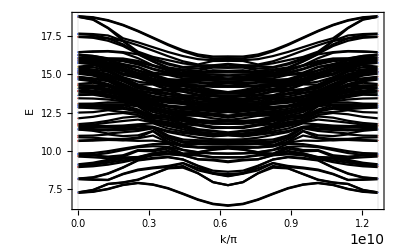

```mathematica
WBandsplit[H1,prsz,{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Max = 0.999

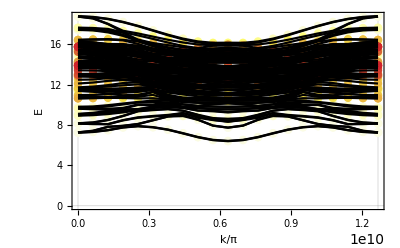

```mathematica
WBands[H1,prfm,{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Min = -0.143, Max = 0.143

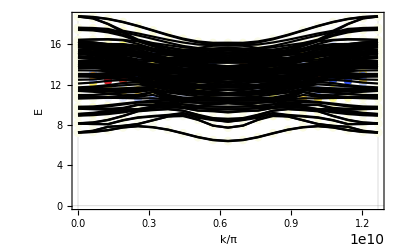

```mathematica
WBands[H1,sxL[3],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Min = -0.757, Max = 0.757

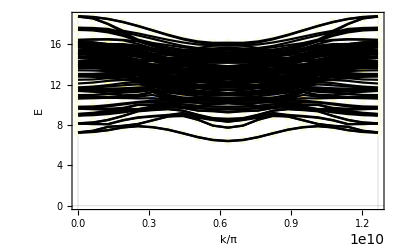

```mathematica
WBands[H1,sxL[9],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```